# This for double Reed. The goal of this notebook is to check stability conditions and to understand power, mass flow rate, assuming some waveform.

```mathematica
Clear["Global`*"]
```

```mathematica
(*c1=1.5 Sqrt[3]);*)
```

```mathematica
(*vdotMax:=(2/3)*w*h0*Sqrt[(2*ΔPMax)/(3*ρ)];
ΔPMax:=(h0*kReed)/ASurface; *)
```

We need two sets of Reed parameters, because the asymmetry of the valve could be important. Set c1=1 because it is just a scaling factor. Below are some design parameters for illustration.

```mathematica
(*vdotMaxIn=2;ΔPMaxIn=1.5;
vdotMaxOut=1.46;ΔPMaxOut=2.5;
Pin = 2;Pout=-2;*)
vdotMaxIn=1;ΔPMaxIn=50;
vdotMaxOut=1*1.1885474446385567;ΔPMaxOut=50;
Pin = 575;Pout=425;
γ=1.4;(*for air*) nout=1; (*again normalizing*)
```

```mathematica
(*Sin with adjustable P_ave and P_mag, fix period as it is not so important*)deltaPReed$Test[t_,Pave_,Pmag_]:=t+0*Pave*Pmag;
deltaPReed$Sin[t_,Pave_,Pmag_]:=Pmag*Sin[2Pi*t]+Pave;
deltaPReed$Drift[t_,Pave_,Pmag_]:=Pmag*Sin[2Pi*t]+Pave+2*t;
```

```mathematica
vReedDotIn[t_,Pave_,Pmag_,Pbdry_,vdotMax_,ΔPMax_, deltaPfunc_]:=Module[{deltaP=Pbdry-deltaPfunc[t,Pave,Pmag]},(*ΔP_reed(t)*)Piecewise[{{-vdotMax  (1-deltaP/ΔPMax) √(1/ΔPMax) √Abs[deltaP],deltaP<=0},{vdotMax*(1-deltaP/ΔPMax)*Sqrt[deltaP/ΔPMax],0<deltaP<ΔPMax},{0,deltaP>=ΔPMax}}]] 
(*Extend the original expression to account for negative flow (ΔP<0) The equation generalizes well, after we make sure the sign is right and take absolute value*)
vReedDotOut[t_,Pave_,Pmag_,Pbdry_,vdotMax_,ΔPMax_,deltaPfunc_]:=Module[{deltaP= deltaPfunc[t,Pave,Pmag]-Pbdry},(*ΔP_reed(t)*)Piecewise[{{vdotMax  (1-deltaP/ΔPMax) √(1/ΔPMax) √Abs[deltaP],deltaP<=0},{-vdotMax*(1-deltaP/ΔPMax)*Sqrt[deltaP/ΔPMax],0<deltaP<ΔPMax},{0,deltaP>=ΔPMax}}]] (*This is negative of the formula, also reorder subtraction*)
```

# but what is EXACTLY the stability condition for a decrease in oscillation amplitude? Below are analysis using mass flow rate (instead of volumetric flow rate)

For isoentropic process and ideal gas, we have p2 = p1(p2/p1), V2 = V1(p2/p1)(−1/γ), T2 = T1(p2/p1)^((γ − 1)/γ). Thus we can solve for the ratio n1/n2to be

```mathematica
P1 = 575;P2=425; (*Data from Nate's paper*)
P1$Pa = P1 * 1000;P2$Pa = P2 * 1000; (*in Pa, kg*m^-1*s^-2*)
T1 = 300; (*room temperature*)

density$ratio = (P1*V1)/(R*T1)*((P2*V1*(P2/P1)^(-1/γ))/(R*T1*(P2/P1)^((1-γ)/γ)))^-1;(*(P1^2(P2/P1)^(2/γ))/P2^2*)
T2 = (P2/P1)^((γ-1)/γ)*T1; (*the cooled temperature*)
ρ$nitrogen1 = 1.145;(*at room temperature and atmospheric pressure. Unit: kg/m^3*)
ρ$nitrogen2 = 1.145/density$ratio;
cp = 1040 ;(*unit: J/(kg*K)*)
```

```mathematica
nin = nout*density$ratio
```

1.18855

```mathematica
density$ratio
```

1.18855

```mathematica
T2
```

275.178

## the MASS FLOW RATE should be the same for inlet valve and outlet valve, otherwise the average pressure in the resonator will change.

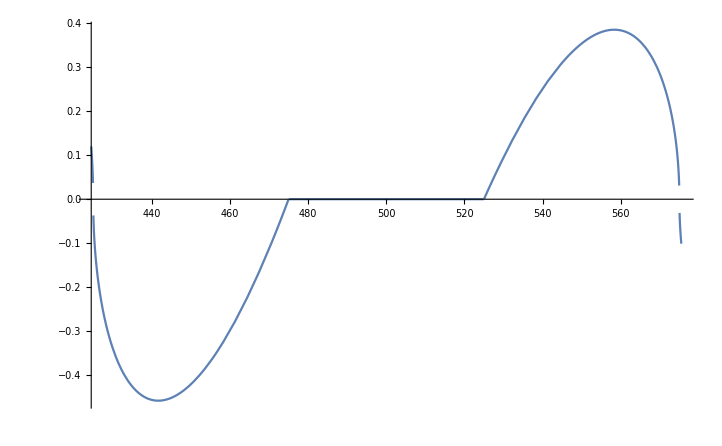

```mathematica
Plot[vReedDotIn[t,425,575,Pin,vdotMaxIn,ΔPMaxIn,deltaPReed$Test],{t,Pout+-0.5,Pin+0.5}]
```

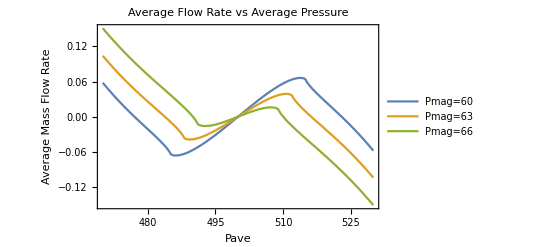

```mathematica
TotalMassFlowRate[ Pave_,Pmag_,deltaPfunc_]:= NIntegrate[nin*vReedDotIn[t,Pave,Pmag,Pin,vdotMaxIn,ΔPMaxIn,deltaPfunc]+nout*vReedDotOut[t,Pave,Pmag,Pout,vdotMaxOut,ΔPMaxOut,deltaPfunc],{t,0,1}]

Plot[{TotalMassFlowRate[Pave,60,deltaPReed$Sin],TotalMassFlowRate[Pave,63,deltaPReed$Sin],TotalMassFlowRate[Pave,66,deltaPReed$Sin]},{Pave,470,530},PlotLegends->{"Pmag=60","Pmag=63","Pmag=66"},Frame->True,FrameLabel->{"Pave","Average Mass Flow Rate"},PlotLabel->"Average Flow Rate vs Average Pressure",BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
(*Making the valves symmetric in mass flow rate is easy. Just make sure the height of the output is multiple but the correct density factor*)
```

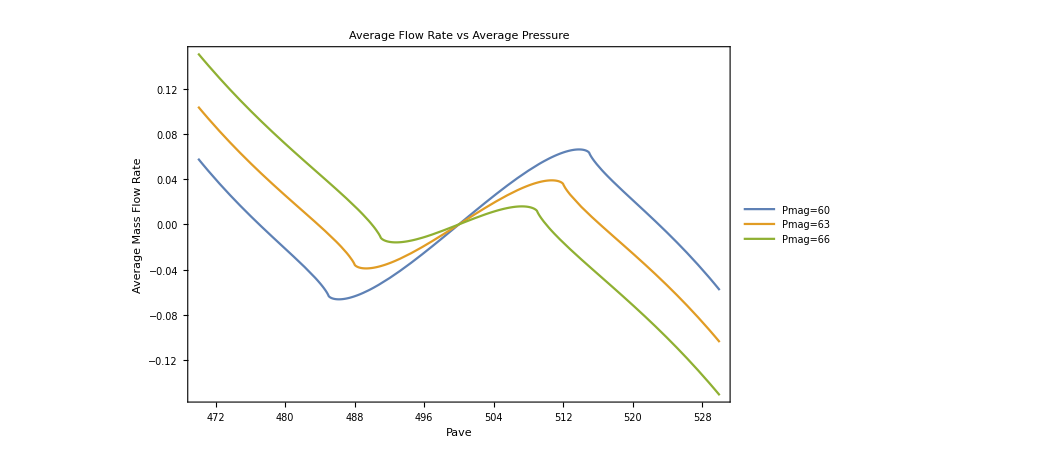

```mathematica
Flow$At$Time[t_,Pave_,Pmag_,deltaPfunc_] :=nin*vReedDotIn[t,Pave,Pmag,Pin,vdotMaxIn,ΔPMaxIn,deltaPfunc]+nout*vReedDotOut[t,Pave,Pmag,Pout,vdotMaxOut,ΔPMaxOut,deltaPfunc] ;
```

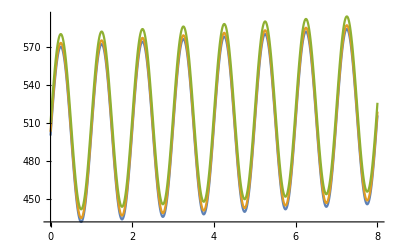

```mathematica
Plot[{deltaPReed$Drift[t,500,70],deltaPReed$Drift[t,503,70],deltaPReed$Drift[t,510,70]},{t,0,8}]
```

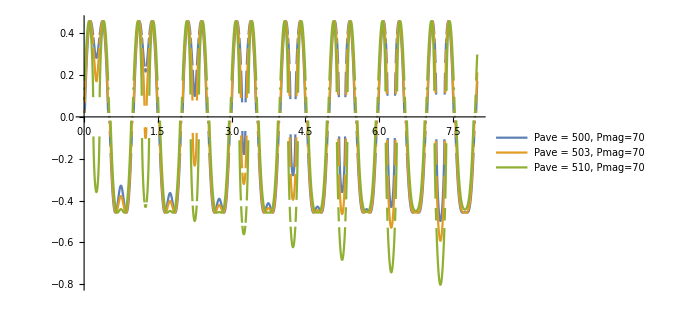

```mathematica
Plot[{Flow$At$Time[t,500,70,deltaPReed$Drift],Flow$At$Time[t,503,70,deltaPReed$Drift],Flow$At$Time[t,510,70,deltaPReed$Drift]},{t,0,8},PlotLegends->{"Pave = 500, Pmag=70","Pave = 503, Pmag=70","Pave = 510, Pmag=70"}]
```

## Below, I would like to compare ΔP * Vdot (this is acoustic work) and mdot * Cp * T (enthalpy flow)

```mathematica
AcousticPower$In[t_,Pave_,Pmag_,Pbdry_,vdotMax_,ΔPMax_, deltaPfunc_]:=vReedDotIn[t,Pave,Pmag,Pbdry,vdotMax,ΔPMax, deltaPfunc]*Abs[(Pbdry-deltaPfunc[t,Pave,Pmag])]*1000;
AcousticPower$Out[t_,Pave_,Pmag_,Pbdry_,vdotMax_,ΔPMax_,deltaPfunc_]:=vReedDotOut[t,Pave,Pmag,Pbdry,vdotMax,ΔPMax, deltaPfunc]*Abs[(Pbdry-deltaPfunc[t,Pave,Pmag])]*1000;
```

```mathematica
EnthalpyFlow$In[t_,Pave_,Pmag_,Pbdry_,vdotMax_,ΔPMax_, deltaPfunc_]:=vReedDotIn[t,Pave,Pmag,Pbdry,vdotMax,ΔPMax, deltaPfunc]*ρ$nitrogen1*cp*T1;
(*Assuming gas at inlet valve is just nitrogen at room temperature*)
EnthalpyFlow$Out[t_,Pave_,Pmag_,Pbdry_,vdotMax_,ΔPMax_, deltaPfunc_]:=vReedDotOut[t,Pave,Pmag,Pbdry,vdotMax,ΔPMax, deltaPfunc]*ρ$nitrogen1/((P1^2(deltaPfunc[t,Pave,Pmag]/P1)^(2/γ))/deltaPfunc[t,Pave,Pmag]^2)*cp*(deltaPfunc[t,Pave,Pmag]/P1)^((γ-1)/γ)*T1; (*!!!!calculate temperature, density as a function of pressure!!!!*)
```

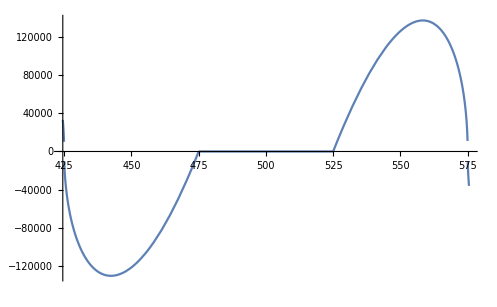

```mathematica
Plot[EnthalpyFlow$In[t,425,575,Pin,vdotMaxIn,ΔPMaxIn,deltaPReed$Test]+EnthalpyFlow$Out[t,0,0,Pout,vdotMaxOut,ΔPMaxOut,deltaPReed$Test],{t,Pout+-0.5,Pin+0.5}]
```

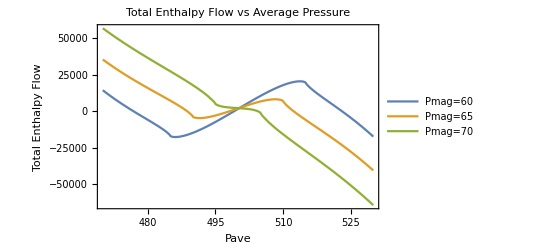

```mathematica
(*AdjustedEnthalpyFlow[ t_,Pave_,Pmag_,deltaPfunc_]:=EnthalpyFlow$In[t,Pave,Pmag,Pin,vdotMaxIn,ΔPMaxIn,deltaPfunc]*Boole[]+EnthalpyFlow$Out[t,Pave,Pmag,Pout,vdotMaxOut,ΔPMaxOut,deltaPfunc]*)

TotalEnthalpyFlow[ Pave_,Pmag_,deltaPfunc_]:= NIntegrate[EnthalpyFlow$In[t,Pave,Pmag,Pin,vdotMaxIn,ΔPMaxIn,deltaPfunc]+EnthalpyFlow$Out[t,Pave,Pmag,Pout,vdotMaxOut,ΔPMaxOut,deltaPfunc],{t,0,1}];
TotalAcousticPower[ Pave_,Pmag_,deltaPfunc_]:= NIntegrate[AcousticPower$In[t,Pave,Pmag,Pin,vdotMaxIn,ΔPMaxIn,deltaPfunc]+AcousticPower$Out[t,Pave,Pmag,Pout,vdotMaxOut,ΔPMaxOut,deltaPfunc],{t,0,1}];

Plot[{TotalEnthalpyFlow[Pave,60,deltaPReed$Sin],TotalEnthalpyFlow[Pave,65,deltaPReed$Sin],TotalEnthalpyFlow[Pave,70,deltaPReed$Sin]},{Pave,470,530},PlotLegends->{"Pmag=60","Pmag=65","Pmag=70"},Frame->True,FrameLabel->{"Pave","Total Enthalpy Flow"},PlotLabel->"Total Enthalpy Flow vs Average Pressure",BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
(*ADD QUALITY FACTOR*)
```

## In actuality, it seems like the oscillation stabilizes with an average slightly larger than the average of the two end pressures (see Jacob Figure 4.23 and Nate Fig 4). I think we will need to figure out what that “stable oscillation pressure” is? --- This is purely just due to the fact that the temperature/density is different at two ends of the valves. And the stable point is the point with zero mass flow.

## Now, I want to check that, what is the thing that drives the initial increase in oscillation. For this I need the valves overlapping each other (i think).

```mathematica
vdotMaxIn=1;ΔPMaxIn=45;
vdotMaxOut=1*1.1885474446385567;ΔPMaxOut=45;
Pin = 600;Pout=545;
1145/2.0
```

572.5

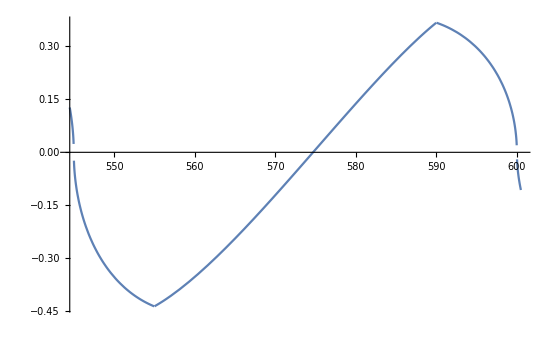

```mathematica
Plot[vReedDotIn[t,425,575,Pin,vdotMaxIn,ΔPMaxIn,deltaPReed$Test]+vReedDotOut[t,0,0,Pout,vdotMaxOut,ΔPMaxOut,deltaPReed$Test],{t,Pout+-0.5,Pin+0.5}]
```

```mathematica
Plot[{TotalEnthalpyFlow[572.5,Pmag,deltaPReed$Sin],TotalEnthalpyFlow[562.5,Pmag,deltaPReed$Sin],TotalEnthalpyFlow[505,Pmag,deltaPReed$Sin],TotalEnthalpyFlow[510,Pmag,deltaPReed$Sin]},{Pmag,10,50},Frame->True,PlotLegends->{"Pave = 500","Pave = 495","Pave=505","Pave = 510"},FrameLabel->{"Pmag","Work Per Cycle"},PlotLabel->"Enthalpy flow per cycle vs Oscillation Amplitude",BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
```

$Aborted

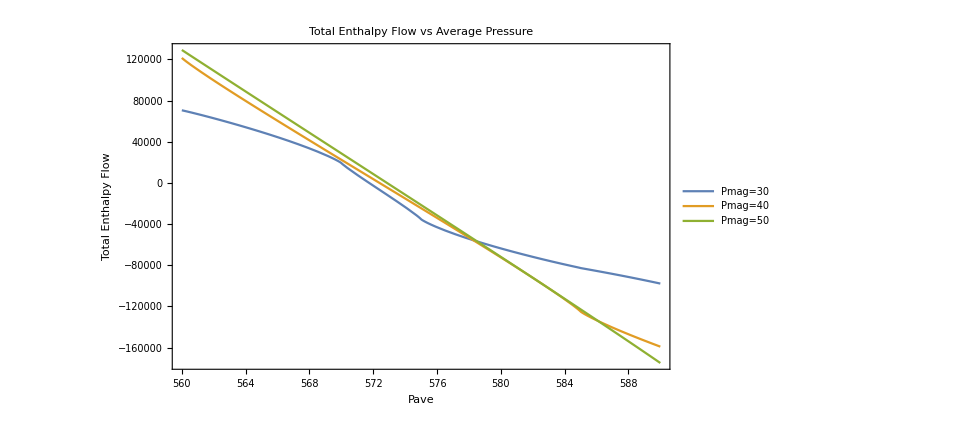

```mathematica
Plot[{TotalEnthalpyFlow[Pave,30,deltaPReed$Sin],TotalEnthalpyFlow[Pave,40,deltaPReed$Sin],TotalEnthalpyFlow[Pave,50,deltaPReed$Sin]},{Pave,560,590},PlotLegends->{"Pmag=30","Pmag=40","Pmag=50"},Frame->True,FrameLabel->{"Pave","Total Enthalpy Flow"},PlotLabel->"Total Enthalpy Flow vs Average Pressure",BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
(*ADD QUALITY FACTOR*)
```

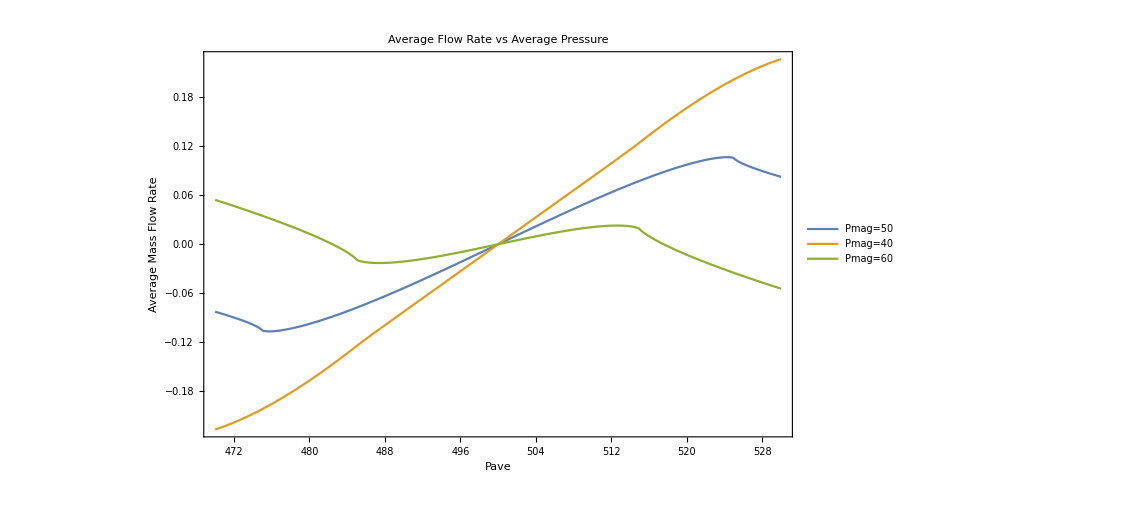

```mathematica
Plot[{TotalMassFlowRate[Pave,50,deltaPReed$Sin],TotalMassFlowRate[Pave,40,deltaPReed$Sin],TotalMassFlowRate[Pave,60,deltaPReed$Sin]},{Pave,470,530},PlotLegends->{"Pmag=50","Pmag=40","Pmag=60"},Frame->True,FrameLabel->{"Pave","Average Mass Flow Rate"},PlotLabel->"Average Flow Rate vs Average Pressure",BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
```

## Q factor and the Vdotmax of the valves can affect the waveform (the amplitude of the wave)

```mathematica
5*Boole[(3>0&&1>-1)]
```

5